{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→10,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

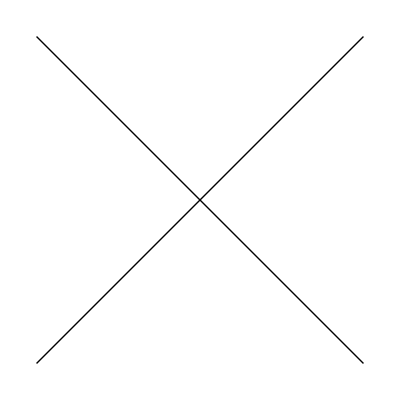
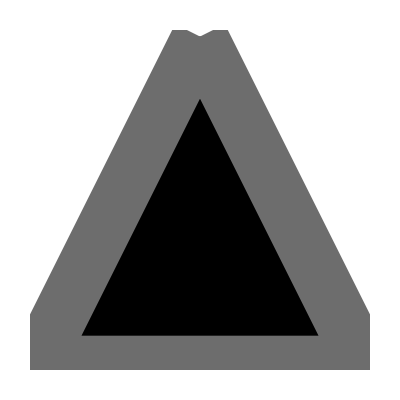
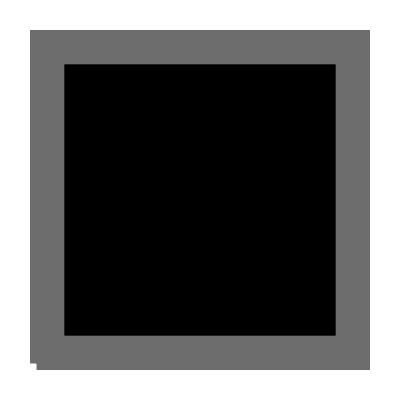
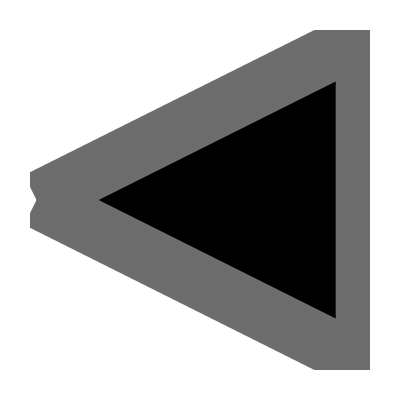
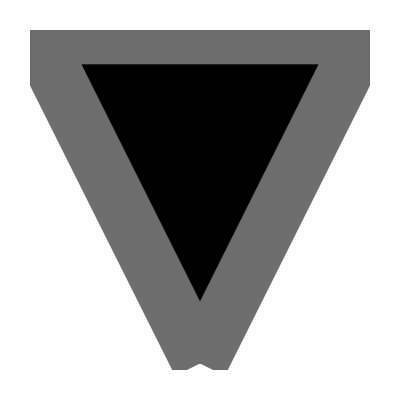
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
<<MaTeX`
myblue=RGBColor[0.2745098039,0.5333333333,0.9450980392];
myred=RGBColor[0.9176470588,0.2588235294,0.2078431373];
mygreen=RGBColor[0.2039215686,0.662745098,0.3176470588];
myyellow=RGBColor[0.9764705882,0.7333333333,0.1764705882];
mygray=RGBColor[109/255//N,109/255//N,109/255//N];
mylightgray=RGBColor[185/255//N,185/255//N,185/255//N];
thickness=0.015;
size=0.05;
font="Latin Modern Roman";
imagSize=200;
fontSize=10;
markersize=0.025;
cm=72/2.54;
ts=0.02*{1,1/GoldenRatio};

SetOptions[MaTeX,FontSize->fontSize]
SetOptions[MatrixPlot,FrameTicksStyle->Black,FrameStyle->Directive[FontFamily->font,FontSize->fontSize,FontColor->Black],ImageSize->imagSize,AspectRatio->1];
SetOptions[ListPlot,FrameStyle->Directive[FontFamily->font,FontSize->fontSize,FontColor->Black],Frame->True,Axes->False,ImageSize->imagSize,GridLines->Automatic,AspectRatio->1,FrameTicksStyle->Black,
PlotStyle->{{Thickness[thickness],myyellow},{Thickness[thickness],myblue},{Thickness[thickness],myred},{Thickness[thickness],mygreen}},Joined->True];
SetOptions[ListPlot,FrameStyle->Directive[FontFamily->font,FontSize->fontSize,FontColor->Black],Frame->True,Axes->False,ImageSize->imagSize,GridLines->Automatic,AspectRatio->1,FrameTicksStyle->Black,
PlotStyle->{{Thickness[thickness],myyellow},{Thickness[thickness],myblue},{Thickness[thickness],myred},{Thickness[thickness],mygreen}},Joined->True];
SetOptions[ListDensityPlot,FrameStyle->Directive[FontFamily->font,FontSize->fontSize,FontColor->Black],Frame->True,Axes->False,ImageSize->imagSize,GridLines->Automatic,AspectRatio->1,FrameTicksStyle->Black];
SetOptions[Plot,FrameStyle->Directive[FontFamily->font,FontSize->fontSize,FontColor->Black],Frame->True,Axes->False,ImageSize->imagSize,GridLines->Automatic,AspectRatio->1,FrameTicksStyle->Black,
PlotStyle->{{Thickness[thickness],myyellow},{Thickness[thickness],myblue},{Thickness[thickness],myred},{Thickness[thickness],mygreen}}];
SetOptions[DensityPlot,FrameStyle->Directive[FontFamily->font,FontSize->fontSize,FontColor->Black],Frame->True,Axes->False,ImageSize->imagSize,GridLines->Automatic,AspectRatio->1,FrameTicksStyle->Black];
align = Sequence[AlignmentPoint -> {0, 0}, AxesOrigin -> {0, 0}, BaselinePosition -> Axis];
size = Sequence[PlotRange -> {{-2, 2}, {-2, 2}}, PlotRangePadding -> Scaled[edgeThickness/2 + plotRangePadding], ImagePadding -> 0, ImageMargins -> 0];
plotRangePadding = .01;
edgeThickness = .1;
size = Sequence[PlotRange -> {{-2, 2}, {-2, 2}}, PlotRangePadding -> Scaled[edgeThickness/2 + plotRangePadding], ImagePadding -> 0, ImageMargins -> 0];
halfTr = {Graphics[{EdgeForm[{mygray, Thickness[edgeThickness], JoinForm["Round"]}], Line[{{-1, -1}, {1, 1}}], Line[{{-1, 1}, {1, -1}}](*EdgeForm[],FaceForm[Opacity[1]],Polygon[{{0,2},{2/Sqrt[3],0},{-(2/Sqrt[3]),0}}],EdgeForm[{Opacity[1],Thickness[edgeThickness],JoinForm["Round"]}],FaceForm[],Polygon[{{0,2},{Sqrt[3],-1},{-Sqrt[3],-1}}]*)}, align],
   Graphics[{EdgeForm[{mygray, Thickness[edgeThickness], JoinForm["Round"]}], Polygon[{{0, 1}, {1, -1}, {-1, -1}}]}, align],
   Graphics[{EdgeForm[{mygray, Thickness[edgeThickness], JoinForm["Round"]}], Rectangle[{-1, -1}, {1, 1}]}, align]};
halfTr = Flatten[{halfTr, Table[halfTr /. p : {_?NumericQ, _?NumericQ} :> RotationMatrix[θ].p, {θ, {Pi/2,  Pi}}]}, 2] /. "size" -> size
Magnify[#, .1] & /@ halfTr;
ListPlot[Flatten[Table[{{n, y}}, {y, Range[1, 3]}, {n, 20}], 1], PlotMarkers -> Table[{s, 0.07}, {s, halfTr}], PlotStyle -> ColorData[60, "ColorList"], GridLines -> {Range[20], Range[3]}, PlotRange -> {{0, 21}, {0, 4}}, Axes -> False, Frame -> True];

new={{"GoogleGradient","",{}},{"Gradients"},1,{0,1},{myblue,Lighter[myblue,.5],Lighter[myblue,.75],White,Lighter[myred,.75],Lighter[myred,.5],myred},""};
ColorData["GoogleGradient"]//Quiet;
AppendTo[DataPaclets`ColorDataDump`colorSchemes,new];
AppendTo[DataPaclets`ColorDataDump`colorSchemeNames,new[[1,1]]];
```

```mathematica
data[[16;;;;31,1]]
```

```mathematica
SetDirectory[NotebookDirectory[]<>"JJpr1_Upar0"];
data=Import["N0032.M0032.coupl+0.000E+00.ES.dat"];
data2=Import["N0032.M0064.coupl+0.000E+00.ES.dat"];
data3=Import["N0032.M0128.coupl+0.000E+00.ES.dat"];
data4=Import["N0032.M0256.coupl+0.000E+00.ES.dat"];
```

```mathematica
legend=LineLegend[(cols={myred,mygreen,myyellow,Black}),MaTeX[{"M=32","M=64","M=128","M=256"}],Spacings->0,LegendMarkerSize->10];
```

```mathematica
sp=16;
ticks={{Join[Table[{i,MaTeX[i],ts},{i,1,3,.25}],Table[{i,"",0.5ts},{i,1.125,3,.25}],{{2,"",ts}},{{2.38,MaTeX["S_A(t)"],ts*0}}],Join[]},{Join[Table[{i,MaTeX[i],ts},{i,0,9,2}],Table[{i,"",0.5ts},{i,1,9,2}],{{9.5,MaTeX["tJ'"],.0}}],{None}}};
plot=Show[ListPlot[{Table[Total[-l*Log2[l]],{l,data[[sp;;;;31,2;;]]^2}],Table[Total[-l*Log2[l]],{l,data2[[sp;;;;31,2;;]]^2}],Table[Total[-l*Log2[l]],{l,data3[[sp;;;;31,2;;]]^2}],Table[Total[-l*Log2[l]],{l,data4[[sp;;;;31,2;;]]^2}]},PlotStyle->cols,GridLines->None,PlotRange->{{0,10},{1.5,2.45}},DataRange->{0,10},FrameTicks->ticks,ImageSize->8.6cm/2,AspectRatio->1,PlotLegends->Placed[legend,{Right,Bottom}]]]
```

```mathematica
Export["entanglement_growth_1.png",plot,ImageResolution->600]
```

```mathematica
sp=14;
ins0=ListPlot[{Table[Total[-l*Log2[l]],{l,data4[[sp;;;;31,2;;]]^2}]},DataRange->{0,10},GridLines->{{},{Log2[8]}},PlotRange->Automatic,PlotStyle->Directive[{Black,Opacity[.8]}]];
sp=12;
ins1=ListPlot[{Table[Total[-l*Log2[l]],{l,data4[[sp;;;;31,2;;]]^2}]},DataRange->{0,10},GridLines->{{},{Log2[8]}},PlotRange->Automatic,PlotStyle->Directive[{Black,Opacity[0.6]}]];
sp=10;
ins2=ListPlot[{Table[Total[-l*Log2[l]],{l,data4[[sp;;;;31,2;;]]^2}]},DataRange->{0,10},GridLines->{{},{Log2[8]}},PlotRange->Automatic,PlotStyle->Directive[{Black,Opacity[0.4]}]];
sp=8;
ins3=ListPlot[{Table[Total[-l*Log2[l]],{l,data4[[sp;;;;31,2;;]]^2}]},DataRange->{0,10},GridLines->{{},{Log2[8]}},PlotRange->Automatic,PlotStyle->Directive[{Black,Opacity[0.2]}]];
sp=16;
plot=Show[ListPlot[{Table[Total[-l*Log2[l]],{l,data4[[sp;;;;31,2;;]]^2}]},PlotStyle->Black,GridLines->None,PlotRange->{{0,10},{1.5,2.45}},DataRange->{0,10},FrameTicks->ticks,ImageSize->8.6cm/2,AspectRatio->1],ins1,ins2,ins3,ins0]
```

```mathematica
Export["entanglement_growth_2.png",plot,ImageResolution->600]
```

```mathematica
SetDirectory[NotebookDirectory[]<>"JJpr1_Upar2"];
data=Import["N0032.M0032.coupl+0.000E+00.ES.dat"];
data2=Import["N0032.M0064.coupl+0.000E+00.ES.dat"];
data3=Import["N0032.M0128.coupl+0.000E+00.ES.dat"];
data4=Import["N0032.M0256.coupl+0.000E+00.ES.dat"];
legend=LineLegend[(cols={myblue,myred,mygreen,myyellow}),MaTeX[{"M=32","M=64","M=128","M=256"}],Spacings->0,LegendMarkerSize->10];
sp=18;
ListPlot[{Table[Total[-l*Log2[l]],{l,data[[sp;;;;31,2;;]]^2}],Table[Total[-l*Log2[l]],{l,data2[[sp;;;;31,2;;]]^2}],Table[Total[-l*Log2[l]],{l,data3[[sp;;;;31,2;;]]^2}],Table[Total[-l*Log2[l]],{l,data4[[sp;;;;31,2;;]]^2}]},GridLines->{{},{Log2[8]}},PlotRange->Automatic]
sp=16;
ticks={{Join[Table[{i,MaTeX[i],ts},{i,0,1.5,.25}],Table[{i,"",0.5ts},{i,0.125,3,.25}],{{2,"",ts}},{{1.675,MaTeX["S_A(t)"],ts*0}}],Join[]},{Join[Table[{i,MaTeX[i],ts},{i,0,9,2}],Table[{i,"",0.5ts},{i,1,9,2}],{{9.5,MaTeX["tJ'"],.0}}],{None}}};
plot=ListPlot[{Table[Total[-l*Log2[l]],{l,data[[sp;;;;31,2;;]]^2}],Table[Total[-l*Log2[l]],{l,data2[[sp;;;;31,2;;]]^2}],Table[Total[-l*Log2[l]],{l,data3[[sp;;;;31,2;;]]^2}],Table[Total[-l*Log2[l]],{l,data4[[sp;;;;31,2;;]]^2}]},PlotStyle->cols,GridLines->None,PlotRange->{{0,10},{0.5,1.75}},DataRange->{0,10},FrameTicks->ticks,PlotLegends->Placed[legend,{Right,Bottom}],AspectRatio->1/GoldenRatio,ImageSize->8.6cm]
```

```mathematica
SetDirectory[NotebookDirectory[]<>"JJpr1_Upar2"];
data=Import["N0032.M0032.coupl+0.000E+00.ES.dat"];
data2=Import["N0032.M0064.coupl+0.000E+00.ES.dat"];
data3=Import["N0032.M0128.coupl+0.000E+00.ES.dat"];
data4=Import["N0032.M0256.coupl+0.000E+00.ES.dat"];
legend=LineLegend[(cols={myred,mygreen,myyellow,Black}),MaTeX[{"M=32","M=64","M=128","M=256"}],Spacings->0,LegendMarkerSize->10];
sp=16;
ticks={{Join[Table[{i,MaTeX[i],ts},{i,0,1.5,.25}],Table[{i,"",0.5ts},{i,0.125,3,.25}],{{2,"",ts}},{{1.675,MaTeX["S_A(t)"],ts*0}}],Join[]},{Join[Table[{i,MaTeX[i],ts},{i,0,9,2}],Table[{i,"",0.5ts},{i,1,9,2}],{{9.5,MaTeX["tJ'"],.0}}],{None}}};
plot=Show[ListPlot[{Table[Total[-l*Log2[l]],{l,data[[sp;;;;31,2;;]]^2}],Table[Total[-l*Log2[l]],{l,data2[[sp;;;;31,2;;]]^2}],Table[Total[-l*Log2[l]],{l,data3[[sp;;;;31,2;;]]^2}],Table[Total[-l*Log2[l]],{l,data4[[sp;;;;31,2;;]]^2}]},PlotStyle->cols,GridLines->None,PlotRange->{{0,10},{0.5,1.75}},DataRange->{0,10},FrameTicks->ticks,ImageSize->8.6cm/2,AspectRatio->1,PlotLegends->Placed[legend,{Right,Bottom}]]]
```

```mathematica
Export["entanglement_growth_3.png",plot,ImageResolution->600]
```

```mathematica
sp=14;
ins0=ListPlot[{Table[Total[-l*Log2[l]],{l,data4[[sp;;;;31,2;;]]^2}]},DataRange->{0,10},GridLines->{{},{Log2[8]}},PlotRange->Automatic,PlotStyle->Directive[{Black,Opacity[.8]}]];
sp=12;
ins1=ListPlot[{Table[Total[-l*Log2[l]],{l,data4[[sp;;;;31,2;;]]^2}]},DataRange->{0,10},GridLines->{{},{Log2[8]}},PlotRange->Automatic,PlotStyle->Directive[{Black,Opacity[0.6]}]];
sp=10;
ins2=ListPlot[{Table[Total[-l*Log2[l]],{l,data4[[sp;;;;31,2;;]]^2}]},DataRange->{0,10},GridLines->{{},{Log2[8]}},PlotRange->Automatic,PlotStyle->Directive[{Black,Opacity[0.4]}]];
sp=8;
ins3=ListPlot[{Table[Total[-l*Log2[l]],{l,data4[[sp;;;;31,2;;]]^2}]},DataRange->{0,10},GridLines->{{},{Log2[8]}},PlotRange->Automatic,PlotStyle->Directive[{Black,Opacity[0.2]}]];
sp=16;
plot=Show[ListPlot[{Table[Total[-l*Log2[l]],{l,data4[[sp;;;;31,2;;]]^2}]},PlotStyle->Black,GridLines->None,PlotRange->{{0,10},{0.5,1.75}},DataRange->{0,10},FrameTicks->ticks,ImageSize->8.6cm/2,AspectRatio->1],ins0,ins1,ins2,ins3]
```

```mathematica
Export["entanglement_growth_4.png",plot,ImageResolution->600]
```

```mathematica
‰
```

```mathematica
ListLogLinearPlot[{Table[Total[-l*Log2[l]],{l,data[[;;31,2;;]]^2}],Table[Total[-l*Log2[l]],{l,data2[[;;31,2;;]]^2}],Table[Total[-l*Log2[l]],{l,data3[[;;31,2;;]]^2}],Table[Total[-l*Log2[l]],{l,data4[[;;31,2;;]]^2}]},GridLines->{{},{Log2[2]}},PlotRange->Automatic]
```

```mathematica
sp=10
ListPlot[{Table[Total[-l*Log2[l]],{l,data[[sp;;;;31,2;;]]^2}],Table[Total[-l*Log2[l]],{l,data2[[sp;;;;31,2;;]]^2}]},GridLines->{{},{Log2[2]}},PlotRange->Full]
sp=16
ListPlot[{Table[Total[-l*Log2[l]],{l,data[[sp;;;;31,2;;]]^2}],Table[Total[-l*Log2[l]],{l,data2[[sp;;;;31,2;;]]^2}]},GridLines->{{},{Log2[2]}},PlotRange->Full]
```

```mathematica
SetDirectory[NotebookDirectory[]<>"uperp/J1.2000"]
data=Import["N0064.M0016.coupl+0.000E+00.ES.dat"];
data2=Import["N0064.M0032.coupl+0.000E+00.ES.dat"];
data3=Import["N0064.M0064.coupl+0.000E+00.ES.dat"];
data4=Import["N0064.M0128.coupl+0.000E+00.ES.dat"];
{Table[-Total[l*Log2[l]],{l,data[[32;;;;63,2;;]]^2}],Table[-Total[l*Log2[l]],{l,data2[[32;;;;63,2;;]]^2}],Table[-Total[l*Log2[l]],{l,data3[[32;;;;63,2;;]]^2}],Table[-Total[l*Log2[l]],{l,data4[[32;;;;63,2;;]]^2}]}//ListPlot
{Table[-Total[l*Log2[l]],{l,data[[2;;31;;2,2;;]]^2}],Table[-Total[l*Log2[l]],{l,data2[[2;;31;;2,2;;]]^2}],Table[-Total[l*Log2[l]],{l,data3[[2;;31;;2,2;;]]^2}],Table[-Total[l*Log2[l]],{l,data4[[2;;31;;2,2;;]]^2}]}//ListLogLinearPlot
```

```mathematica
SetDirectory[NotebookDirectory[]<>"uperp/J1.2000"];
d1=Import["N0064.M0008.coupl+0.000E+00.LM.dat"];
d1 = Partition[d1[[All,{1,4}]],64];
d2=Import["N0064.M0016.coupl+0.000E+00.LM.dat"];
d2 = Partition[d2[[All,{1,4}]],64];
d3=Import["N0064.M0032.coupl+0.000E+00.LM.dat"];
d3 = Partition[d3[[All,{1,4}]],64];
d4=Import["N0064.M0064.coupl+0.000E+00.LM.dat"];
d4 = Partition[d4[[All,{1,4}]],64];
d5=Import["N0064.M0128.coupl+0.000E+00.LM.dat"];
d5 = Partition[d5[[All,{1,4}]],64];
d6=Import["N0064.M0256.coupl+0.000E+00.LM.dat"];
d6 = Partition[d6[[All,{1,4}]],64];
```

```mathematica
X=Table[i-d1[[1,1,1]]/4+If[EvenQ[d1[[1,1,1]]/2],0,-.5],{i,d1[[1,1,1]]/2}];
GammaX=Flatten[{X,-X}ᵀ];
```

```mathematica
{Table[dd[[All,2]].GammaX,{dd,d3}],Table[dd[[All,2]].GammaX,{dd,d4}],Table[dd[[All,2]].GammaX,{dd,d5}],Table[dd[[All,2]].GammaX,{dd,d6}]}//ListPlot
```

```mathematica
Manipulate[ListPlot[{d4[[ii]],d5[[ii]],d6[[ii]]},PlotRange->Full,PlotMarkers->Automatic,PlotStyle->Thin,ImageSize->2*8.6cm],{ii,1,100,1}]
```

```mathematica
SetDirectory[NotebookDirectory[]<>"test/hubbardU6.0000/J0.6000"];
d1=Import["N0064.M0016.coupl+0.000E+00.LM.dat"];
d1 = Partition[d1[[All,{1,4}]],64];
d2=Import["N0064.M0032.coupl+0.000E+00.LM.dat"];
(*d2 = Partition[d2[[All,{1,4}]],64];
d3=Import["N0064.M0064.coupl+0.000E+00.LM.dat"];
d3 = Partition[d3[[All,{1,4}]],64];*)
X=Table[i-d1[[1,1,1]]/4+If[EvenQ[d1[[1,1,1]]/2],0,-.5],{i,d1[[1,1,1]]/2}];
GammaX=Flatten[{X,-X}ᵀ];
{Table[-4dd[[All,2]].GammaX,{dd,d1}],Table[-4dd[[All,2]].GammaX,{dd,d2}],Table[-4dd[[All,2]].GammaX,{dd,d3}]}//ListPlot
```

```mathematica
d1[[1]]
```

```mathematica
tp=Import["N0064.M0032.coupl+0.000E+00.LM.dat"];
```

```mathematica
SetDirectory[NotebookDirectory[]<>"test_TL/hubbardU1.5000/J0.0469/Jpr1.0000"];
d1=Import["N0064.M0032.coupl+0.000E+00.LM.dat"];
d1 = Partition[d1[[All,{1,7}]],64];
d2=Import["N0064.M0064.coupl+0.000E+00.LM.dat"];
d2 = Partition[d2[[All,{1,7}]],64];
d3=Import["N0128.M0064.coupl+0.000E+00.LM.dat"];
d3 = Partition[d3[[All,{1,7}]],128];
d4=Import["N0032.M0032.coupl+0.000E+00.LM.dat"];
d4 = Partition[d4[[All,{1,7}]],32];
(*d2 = Partition[d2[[All,{1,4}]],64];
d3=Import["N0064.M0064.coupl+0.000E+00.LM.dat"];
d3 = Partition[d3[[All,{1,4}]],64];*)
X=Table[i-d2[[1,1,1]]/2,{i,d2[[1,1,1]]}];
ListPlot[{Table[4dd[[All,2]].X,{dd,d1}],Table[4dd[[All,2]].X,{dd,d2}]},PlotMarkers->Automatic,Joined->False]
X=Table[i-d3[[1,1,1]]/2,{i,d3[[1,1,1]]}];
ListPlot[{Table[4dd[[All,2]].X,{dd,d3}]},PlotMarkers->Automatic,Joined->False]
X=Table[i-d4[[1,1,1]]/2,{i,d4[[1,1,1]]}];
ListPlot[{Table[4dd[[All,2]].X,{dd,d4}]},PlotMarkers->Automatic,Joined->False]
```

```mathematica
SetDirectory[NotebookDirectory[]<>"test_TL/hubbardU0.0000/J0.0469/Jpr1.0000"];
d4=Import["N0032.M0032.coupl+0.000E+00.LM.dat"];
d4 = Partition[d4[[All,{1,3}]],32];
X=Table[i-d4[[1,1,1]]/2,{i,d4[[1,1,1]]}]
ListPlot[{Table[4dd[[All,2]].X,{dd,d4}]},PlotMarkers->Automatic,Joined->False,PlotRange->Full]
```

```mathematica
tp=Import["N0032.M0032.coupl+0.000E+00.LM.dat"];
```

```mathematica
L=32;
J=0.0469;
Jpr=1.;
enne=L;
H=ConstantArray[0,{2L,2L}];
Do[
H[[2i-1,2i]]+=J;
,{i,1,L}];
Do[
H[[2i,2i+1]]+=Jpr;
,{i,1,L-1}];
H=H+H†;
{eval,Ug}=Eigensystem[H];
order = Ordering[eval];
eval=eval[[order]];
Ug=Ug[[order]];
Table[Ug[[i]]=Normalize[Ug[[i]]],{i,Length[Ug]}];
{e0,U0, H0}={eval,Ug, H};
e0[[;;enne]]//Total
Q=ConstantArray[0,2L];
qpos=L/2;
Q[[2*qpos-1]]=1;
Chop[U0.H0.U0†]//MatrixPlot;
Chop[U0†.DiagonalMatrix[e0].U0]//MatrixPlot;
P=U0.Q;
Clear[ΩM, ΩP];
ΩP[enne_]:=Norm[P[[enne+1;;]]]^2;
ΩM[enne_]:=Norm[P[[;;enne]]]^2;
(* create the chiral average position operator *)
(* create the chiral average position operator *)
X=Table[i-L/2+If[EvenQ[L],0,-.5],{i,L}]
GammaX=Flatten[{X,-X}ᵀ];
(* time evolution operator in diagonal basis *)
Clear[A];
A[t_,ev_]:=N[DiagonalMatrix[ⅇ^(-ⅈ*ev*t)]];
(* spectrum of the Hamiltonian *)
Show[ListPlot[e0,Joined->False]];
G0=U0ᵀ[[;;,;;enne]].U0*[[;;enne,;;]];
GQP[t_,enne_]:=N[U0ᵀ[[;;,;;enne]].U0*[[;;enne,;;]]+Chop[If[t≥ 0, 1.0, 0.0]*1/ΩP[enne]{(U0†[[;;,enne+1;;]].A[t,e0]*[[enne+1;;,enne+1;;]].P[[enne+1;;]])}ᵀ.{(P*[[enne+1;;]].A[t,e0][[enne+1;;,enne+1;;]].U0[[enne+1;;,;;]])}]];
```

```mathematica
SetDirectory[NotebookDirectory[]<>"test_TL/hubbardU1.5000/J0.0469/Jpr1.0000"];
d1=Import["N0032.M0064.coupl+0.000E+00.LM.dat"];
d1 = Partition[d1[[All,{1,7}]],32];
X=Table[i-d1[[1,1,1]]/2,{i,d1[[1,1,1]]}];
d1=Table[4Reverse[dd[[All,2]]-d1[[1,All,2]]].X,{dd,d1}];

d2=Import["N0064.M0256.coupl+0.000E+00.LM.dat"];
d2 = Partition[d2[[All,{1,7}]],64];
X=Table[i-d2[[1,1,1]]/2,{i,d2[[1,1,1]]}];
d2=Table[4Reverse[dd[[All,2]]-d2[[1,All,2]]].X,{dd,d2}];

d3=Import["N0128.M0064.coupl+0.000E+00.LM.dat"];
d3 = Partition[d3[[All,{1,7}]],128];
X=Table[i-d3[[1,1,1]]/2,{i,d3[[1,1,1]]}];
d3=Table[4Reverse[dd[[All,2]]-d3[[1,All,2]]].X,{dd,d3}];
```

```mathematica
ListPlot[{d1,d2,d3}]
```

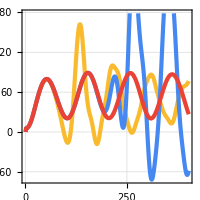

```mathematica
SetDirectory[NotebookDirectory[]<>"test_TL/hubbardU2.7500/J0.0469/Jpr1.0000"];
d1=Import["N0032.M0128.coupl+0.000E+00.LM.dat"];
d1 = Partition[d1[[All,{1,7}]],32];
X=Table[i-d1[[1,1,1]]/2,{i,d1[[1,1,1]]}];
d1=Table[4Reverse[dd[[All,2]]-d1[[1,All,2]]].X,{dd,d1}];

d2=Import["N0064.M0128.coupl+0.000E+00.LM.dat"];
d2 = Partition[d2[[All,{1,7}]],64];
X=Table[i-d2[[1,1,1]]/2,{i,d2[[1,1,1]]}];
d2=Table[4Reverse[dd[[All,2]]-d2[[1,All,2]]].X,{dd,d2}];

d3=Import["N0128.M0128.coupl+0.000E+00.LM.dat"];
d3 = Partition[d3[[All,{1,7}]],128];
X=Table[i-d3[[1,1,1]]/2,{i,d3[[1,1,1]]}];
d3=Table[4Reverse[dd[[All,2]]-d3[[1,All,2]]].X,{dd,d3}];

ListPlot[{d1,d2,d3}]
```

```mathematica
legend1 =LineLegend[{myyellow,myblue,myred},{MaTeX["L=32"],MaTeX["L=64"],MaTeX["L=128"]},LegendLayout->"Row",LegendMarkerSize->15,Spacings->0.5]
```

```mathematica
d1=Import["N0032.M0128.coupl+0.000E+00.LM.dat"];
d1 = Partition[d1[[All,{1,4}]],32];
d2=Import["N0064.M0128.coupl+0.000E+00.LM.dat"];
d2 = Partition[d2[[All,{1,4}]],64];
d3=Import["N0128.M0128.coupl+0.000E+00.LM.dat"];
d3 = Partition[d3[[All,{1,4}]],128];
Manipulate[ListPlot[{d1[[i]],d2[[i]],d3[[i]]},PlotRange->Full],{i,1,Length[d3],1}]
```

```mathematica
ticks={{Join[Table[{i,MaTeX[i-65],ts},{i,5,120,20}],Table[{i,"",0.5*ts},{i,15,120,20}],{{122,MaTeX["x"],ts*0}}],Join[]},{Join[Table[{i,MaTeX[i],ts},{i,0,35,10}],Table[{t,"",0.5*ts},{t,5,40,10}],{{38,MaTeX["tJ'"],.0}}],{None}}};
fs3=Show[ListPlot[{},PlotRange->{{0,40},{1.,128}},AspectRatio->1,FrameTicks->ticks,GridLines->None],ListDensityPlot[d3[[All,All,2]]ᵀ,ColorFunction->"PigeonTones",ColorFunction->"PigeonTones",PlotRange->Full,Frame->True,FrameStyle->Black,DataRange->{{0,40},{1.,128.}},PlotRangePadding->0,GridLines->None,PlotRangePadding->0],ImageSize->8.6cm/2,ImagePadding->(ip={{27,2},{18,2}})]
SetDirectory[NotebookDirectory[]]
Export["creutz_fs_4.png",fs3,ImageResolution->600]
```

```mathematica
legend=LineLegend[(cols={myyellow,myblue,myred,Black}),MaTeX[{"L=32","L=64","L=128"}],Spacings->.0,LegendMarkerSize->10,LegendLayout->"Column"]
```

```mathematica
op=1;
fs=0.2;
p1=ListPlot[d1,DataRange->{0,40},PlotMarkers->None,Joined->True,PlotRange->Full,PlotRangePadding->0,PlotStyle->Thickness[.025],ColorFunction->Function[{x,y},If[x>0.2,{myyellow,Opacity[op(1-(x-.2)^fs)]},myyellow]]];
p2=ListPlot[d2,DataRange->{0,40},PlotMarkers->None,Joined->True,PlotRange->Full,PlotRangePadding->0,PlotStyle->Thickness[.02],ColorFunction->Function[{x,y},If[x>0.5,{myblue,Opacity[op(1-(x-.5)^fs)]},myblue]]];
p3=ListPlot[d3,DataRange->{0,40},PlotMarkers->None,Joined->True,PlotRange->Full,PlotRangePadding->0,PlotStyle->Thickness[.015],ColorFunction->Function[{x,y},If[x>1,{myred,Opacity[op(1-(x-1)^fs)]},myred]]];
ticks={{Join[Table[{i,"",0.5*ts},{i,-25,250,50}],Table[{i,MaTeX[i],ts},{i,-50,150,50}],Table[{i,"",ts},{i,-150,250,50}],Table[{i,"",0.5*ts},{i,-.5,1.5,1}],{{2,"",ts}},{{220,MaTeX["\\Delta\\mathcal C"],ts*0}}],Join[]},{Join[Table[{i,MaTeX[i],ts},{i,0,35,10}],Table[{t,"",0.5*ts},{t,5,40,10}],{{38,MaTeX["tJ'"],.0}}],{None}}};
fs1=Show[p2,p1,p3,FrameTicks->ticks,ImageSize->8.6cm/2,AspectRatio->1,PlotRange->{{0,40},{-75,250}},GridLines->{{{8,Directive[myyellow,Dotted,Thickness[0.025]]},{20,Directive[myblue,Dotted,Thickness[0.025]]}},{}},Epilog->Inset[legend,{41,70},{Right,Bottom}],GridLinesStyle->Directive[{mygray,Thick,Dotted,Opacity[1]}],ImagePadding->(ip={{27,2},{18,2}})]
```

-Graphics-

```mathematica
fs1=Show[-Graphics-,ImageSize->8.6cm/2,GridLines->{{{10,Directive[myyellow,Dotted,Thickness[0.025]]},{20,Directive[myblue,Dotted,Thickness[0.025]]}},{}},Epilog->Inset[legend,{41,70},{Right,Bottom}],GridLinesStyle->Directive[{mygray,Thick,Dotted,Opacity[1]}],ImagePadding->(ip={{27,2},{18,2}})]
```

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]]
Export["creutz_fs_1.png",fs1,ImageResolution->600]
```

/Users/andreas/Desktop

creutz_fs_1.png

```mathematica
d2=Import["N0064.M0128.coupl+0.000E+00.LM.dat"];
d2 = Partition[d2[[All,{1,4}]],64];
Manipulate[ListPlot[d2[[i]],PlotRange->Full],{i,1,Length[d2],1}]
```

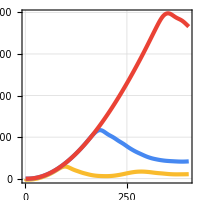

```mathematica
SetDirectory[NotebookDirectory[]<>"test_TL/hubbardU4.5000/J0.0469/Jpr1.0000"];
d1=Import["N0032.M0128.coupl+0.000E+00.LM.dat"];
d1 = Partition[d1[[All,{1,7}]],32];
X=Table[i-d1[[1,1,1]]/2,{i,d1[[1,1,1]]}];
d1=Table[4Reverse[dd[[All,2]]-d1[[1,All,2]]].X,{dd,d1}];

d2=Import["N0064.M0128.coupl+0.000E+00.LM.dat"];
d2 = Partition[d2[[All,{1,7}]],64];
X=Table[i-d2[[1,1,1]]/2,{i,d2[[1,1,1]]}];
d2=Table[4Reverse[dd[[All,2]]-d2[[1,All,2]]].X,{dd,d2}];

d3=Import["N0128.M0128.coupl+0.000E+00.LM.dat"];
d3 = Partition[d3[[All,{1,7}]],128];
X=Table[i-d3[[1,1,1]]/2,{i,d3[[1,1,1]]}];
d3=Table[4Reverse[dd[[All,2]]-d3[[1,All,2]]].X,{dd,d3}];

ListPlot[{d1,d2,d3}]
```

```mathematica
op=1;
fs=0.2;
p1=ListPlot[d1,DataRange->{0,40},PlotMarkers->None,Joined->True,PlotRange->Full,PlotRangePadding->0,PlotStyle->Thickness[.025],ColorFunction->Function[{x,y},If[x>0.2,{myyellow,Opacity[op(1-(x-.2)^fs)]},myyellow]]];
p2=ListPlot[d2,DataRange->{0,40},PlotMarkers->None,Joined->True,PlotRange->Full,PlotRangePadding->0,PlotStyle->Thickness[.02],ColorFunction->Function[{x,y},If[x>0.5,{myblue,Opacity[op(1-(x-.5)^fs)]},myblue]]];
p3=ListPlot[d3,DataRange->{0,40},PlotMarkers->None,Joined->True,PlotRange->Full,PlotRangePadding->0,PlotStyle->Thickness[.015],ColorFunction->Function[{x,y},If[x>.875,{myred,Opacity[op(1-(x-.875)^fs)]},myred]]];
ticks={{Join[Table[{i,"",0.5*ts},{i,1000,8000,2000}],Table[{i,MaTeX[i],ts},{i,0,6000,2000}],{{7600,MaTeX["\\Delta\\mathcal C"],ts*0}},{{8000,"",ts}}],{}},{Join[Table[{i,MaTeX[i],ts},{i,0,35,10}],Table[{t,"",0.5*ts},{t,5,40,10}],{{38,MaTeX["tJ'"],.0}}],{None}}};
```

```mathematica
fs1=Show[p1,p2,p3,FrameTicks->ticks,ImageSize->8.6cm/2,AspectRatio->1,PlotRange->{{0,42},{-500,8200}},GridLines->{{{10,Directive[myyellow,Dotted,Thickness[0.025]]},{20,Directive[myblue,Dotted,Thickness[0.025]]},{35,Directive[myred,Dotted,Thickness[0.025]]}},{}},ImagePadding->(ip={{27,2},{18,2}}),Epilog->Inset[legend,{44,-1000},{Right,Bottom}],GridLinesStyle->Directive[{mygray,Thick,Dotted,Opacity[1]}]]
```

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]]
Export["creutz_fs_2.png",fs1,ImageResolution->600]
```

/Users/andreas/Desktop

creutz_fs_2.png

```mathematica
d1=Import["N0032.M0128.coupl+0.000E+00.LM.dat"];
d1 = Partition[d1[[All,{1,4}]],32];
d2=Import["N0064.M0128.coupl+0.000E+00.LM.dat"];
d2 = Partition[d2[[All,{1,4}]],64];
Manipulate[ListPlot[{d1[[i]],d2[[i]]},PlotRange->Full],{i,1,Length[d2],1}]
```

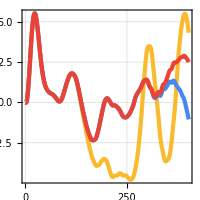

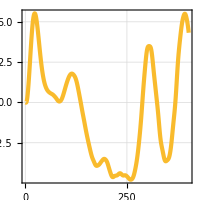

```mathematica
SetDirectory[NotebookDirectory[]<>"test_TL/hubbardU5.5000/J0.4219/Jpr1.0000"];
d1=Import["N0032.M0128.coupl+0.000E+00.LM.dat"];
d1 = Partition[d1[[All,{1,7}]],32];
X=Table[i-d1[[1,1,1]]/2,{i,d1[[1,1,1]]}];
d1=Table[4Reverse[dd[[All,2]]-d1[[1,All,2]]].X,{dd,d1}];

d2=Import["N0064.M0128.coupl+0.000E+00.LM.dat"];
d2 = Partition[d2[[All,{1,7}]],64];
X=Table[i-d2[[1,1,1]]/2,{i,d2[[1,1,1]]}];
d2=Table[4Reverse[dd[[All,2]]-d2[[1,All,2]]].X,{dd,d2}];

d3=Import["N0128.M0128.coupl+0.000E+00.LM.dat"];
d3 = Partition[d3[[All,{1,7}]],128];
X=Table[i-d3[[1,1,1]]/2,{i,d3[[1,1,1]]}];
d3=Table[4Reverse[dd[[All,2]]-d3[[1,All,2]]].X,{dd,d3}];

ListPlot[{d1,d2,d3}]
d1//ListPlot
```

```mathematica
d1=Import["N0032.M0128.coupl+0.000E+00.LM.dat"];
d1 = Partition[d1[[All,{1,4}]],32];
d2=Import["N0064.M0128.coupl+0.000E+00.LM.dat"];
d2 = Partition[d2[[All,{1,4}]],64];
d3=Import["N0128.M0128.coupl+0.000E+00.LM.dat"];
d3 = Partition[d3[[All,{1,4}]],128];
Manipulate[ListPlot[{d1[[i]],d2[[i]],d3[[i]]},PlotRange->Full],{i,1,Length[d3],1}]
```

Part::partd: Part specification d1⟦402⟧ is longer than depth of object.

Part::partd: Part specification d2⟦402⟧ is longer than depth of object.

Part::partd: Part specification d3⟦402⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
ticks={{Join[Table[{i,MaTeX[i-65],ts},{i,5,120,20}],Table[{i,"",0.5*ts},{i,15,120,20}],{{122,MaTeX["x"],ts*0}}],Join[]},{Join[Table[{i,MaTeX[i],ts},{i,0,35,10}],Table[{t,"",0.5*ts},{t,5,40,10}],{{38,MaTeX["tJ'"],.0}}],{None}}};
fs3=Show[ListPlot[{},PlotRange->{{0,40},{1.,128}},AspectRatio->1,FrameTicks->ticks],ListDensityPlot[d3[[All,All,2]]ᵀ,ColorFunction->"PigeonTones",ColorFunction->"PigeonTones",PlotRange->Full,Frame->True,FrameStyle->Black,DataRange->{{0,40},{1.,128.}},PlotRangePadding->0,GridLines->None,PlotRangePadding->0],ImageSize->8.6cm/2,ImagePadding->(ip={{27,2},{18,2}})]
SetDirectory[NotebookDirectory[]]
Export["creutz_fs_3.png",fs3,ImageResolution->600]
```